```mathematica
Integrate[Integrate[x^2+y^2, {y, 1,2}], {x, 2, 2.1}]
```

0.653667

```mathematica
N[Integrate[4+y^2, {y, 1,2}]/10]
```

0.633333

```mathematica
N[Integrate[2+y^2, {y, 1,2}]/10]
```

0.433333

```mathematica
Integrate[Integrate[r^3, {r, 0 ,2}], {t, 0, Pi}]
```

4 π

```mathematica
Integrate[Integrate[r^5, {r, 1 ,2}], {t, 0, 2*Pi}]
```

21 π

```mathematica
Integrate[Integrate[y, {y,0,x}], {x, 0, 2}]
```

4/3

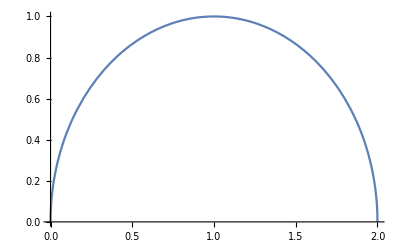

```mathematica
Plot[x=Sqrt[2*y-y^2], {y, 0, 2}]
```

```mathematica
Integrate[Integrate[r*t^2,{r,0,2}],{t, 0, Pi/2}]/Pi
```

π^2/12

```mathematica
Clear[x]
Integrate[Integrate[(x^2+y)/(x+y^2), {x,10,13}], {y, 1,1.1}]
```

3.1733

```mathematica
Integrate[r^4*Cos[t], {r, 0, 5}]
```

625 Cos[t]

```mathematica
Integrate[-625*Cos[t], {t, Pi/2, 3*Pi/2}]
```

1250

```mathematica
B =Integrate[Integrate[x^2/30^2, {x, 0,15}], {y, 0, 30}];
A =Integrate[Integrate[1-x^2/30^2, {x, 0,15}], {y, 0, 30}];
AP = A/(A+B)*100;
BP = B/(A+B)*100;
AP
BP
AP-BP
```

275/3

25/3

250/3

```mathematica
B2 =Integrate[Integrate[x^2/30^2, {x, 15,30}], {y, 0, 15}];
A2 =Integrate[Integrate[1-x^2/30^2, {x, 15,30}], {y, 0, 15}];
AP2 = A2/(A2+B2)*100;
BP2= B2/(A2+B2)*100;
AP2
BP2
AP2-BP2
```

125/3

175/3

-50/3

```mathematica
B3 =Integrate[Integrate[x^2/30^2, {x, 15,30}], {y, 15, 30}];
A3 =Integrate[Integrate[1-x^2/30^2, {x, 15,30}], {y, 15, 30}];
AP3 = A3/(A3+B3)*100;
BP3= B3/(A3+B3)*100;
AP3
BP3
AP3-BP3
```

125/3

175/3

-50/3

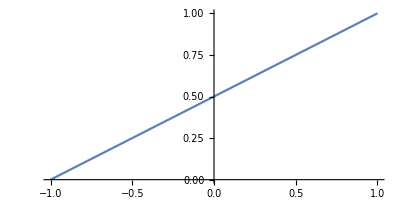

```mathematica
ParametricPlot[{2*t-1, t}, {t, 0,1}]
```